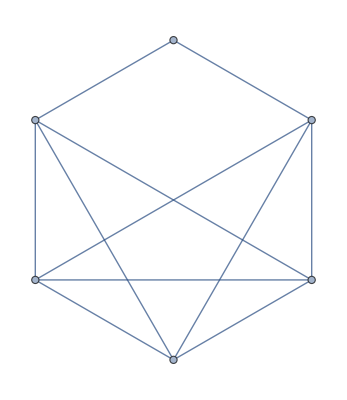

```mathematica
gr=EdgeAdd[EdgeDelete[CompleteGraph[5],1<->5],{1<->6,5<->6}]
```

```mathematica
Select[Keys[allGraphs6],Sort[EdgeList[allGraphs6[#,"graph"]]]==Sort[EdgeList[gr]]&]
```

{6996547}

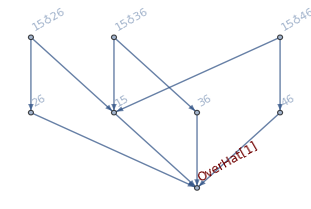

```mathematica
allGraphs6[6996547,"colofour"]//FormulaGraphReverse
```

```mathematica
ChromaticPolynomial[allGraphs6[6996547,"graph"],x]//Factor
```

(-3+x) (-2+x) (-1+x) x (7-5 x+x^2)

```mathematica
Eliminate[x==a^3+9b^3-c^3&&y==9b^3+c^3-a^3&&z==9b^3+c^3+a^3&&p==z^3-x^3-y^3,{x,y,z}]
```

p==a^9-27 a^6 b^3+243 a^3 b^6-729 b^9+3 a^6 c^3+162 a^3 b^3 c^3+243 b^6 c^3+3 a^3 c^6-27 b^3 c^6+c^9

```mathematica
Plot[,
```

```mathematica
Solve[p==a^9-27 a^6 b^3+243 a^3 b^6-729 b^9+3 a^6 c^3+162 a^3 b^3 c^3+243 b^6 c^3+3 a^3 c^6-27 b^3 c^6+c^9==0,{a,b,c}]
```

{}

```mathematica
Eliminate[x==a^3+9b^3-c^3&&y==9b^3+c^3-a^3&&z==9b^3+c^3+a^3&&p==z^3-x^3,{x,y,z}]
```

p==c^3 (6 a^6+108 a^3 b^3+486 b^6+2 c^6)

```mathematica
Factor[2 a^9+486 a^3 b^6-6 a^6 c^3-486 b^6 c^3+6 a^3 c^6-2 c^9]
```

2 (a-c) (a^2+a c+c^2) (a^6+243 b^6-2 a^3 c^3+c^6)

```mathematica
Factor[a^9-27 a^6 b^3+243 a^3 b^6-729 b^9+3 a^6 c^3+162 a^3 b^3 c^3+243 b^6 c^3+3 a^3 c^6-27 b^3 c^6+c^9]
```

(a^3-9 b^3+6 a b c+c^3) (a^6-18 a^3 b^3+81 b^6-6 a^4 b c+54 a b^4 c+36 a^2 b^2 c^2+2 a^3 c^3-18 b^3 c^3-6 a b c^4+c^6)

```mathematica
(a^3-9 b^3+6 a b c+c^3) (a^6-18 a^3 b^3+81 b^6-6 a^4 b c+54 a b^4 c+36 a^2 b^2 c^2+2 a^3 c^3-18 b^3 c^3-6 a b c^4+c^6)
Factor[a^3 (2 a^6+486 b^6+108 b^3 c^3+6 c^6)]
```

(a^3-9 b^3+6 a b c+c^3) (a^6-18 a^3 b^3+81 b^6-6 a^4 b c+54 a b^4 c+36 a^2 b^2 c^2+2 a^3 c^3-18 b^3 c^3-6 a b c^4+c^6)

2 a^3 (a^6+243 b^6+54 b^3 c^3+3 c^6)